ï.8e£

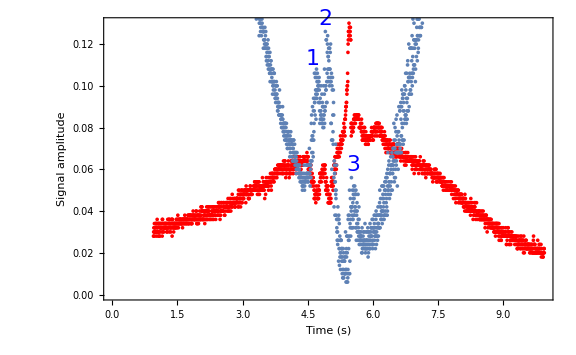
{1.67422×10^7 (ï.8e£)^13 Null^9 -Graphics-,1360.72 (ï.8e£)^13 Null^9 -Graphics-}

```mathematica
SetDirectory[NotebookDirectory[]];
ï.8e£
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];ï.8e£Show[ListPlot[Map[{#[[1]],#[[2]]*5-0.0388*5+0.2}&,pd],PlotStyle->Red],ListPlot[Map[{#[[1]],#[[2]]-1.17+0.2 }&,las]],Graphics[Text[Style["1",FontSize->22,FontColor->Blue],{4.6,0.113}]],Graphics[Text[Style["2",FontSize->22,FontColor->Blue],{4.9,0.132}]],Graphics[Text[Style["3",FontSize->22,FontColor->Blue],{5.55,0.062}]],Graphics[Text[Style["MOT",FontSize->18,FontColor->Red],{5.6,0.1345}]],Axes -> {True, False}, Frame->{{True,False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Signal amplitude",Medium]}, ImageSize->Large]ï.8e£p1 = {4.708,0.024};ï.8e£p2 = {4.956, 0.024};ï.8e£p3 = {5.556, 0.016};ï.8e£d12 = 31.7;ï.8e£d23 = 60.3;ï.8e£C12 = {(p2[[1]]-p1[[1]])/d12, Sqrt[p2[[2]]^2 + p1[[2]]^2]/d12 };ï.8e£C23 = {(p3[[1]]-p2[[1]])/d23, Sqrt[p3[[2]]^2 + p2[[2]]^2]/d23 };ï.8e£Cinv12 = {1/C12[[1]],1/C12[[1]]^2 * C12[[2]]}ï.8e£Cinv23 = {1/C23[[1]],1/C23[[1]]^2 * C23[[2]]}ï.8e£CinvAvg = {Mean[{Cinv12[[1]],Cinv23[[1]]}],Mean[{Cinv12[[2]],Cinv23[[2]]}]}ï.8e£mot = {0.1, 0.008};ï.8e£Î.94 = {mot[[1]]*CinvAvg[[1]],Sqrt[mot[[1]]^2*CinvAvg[[2]]^2 + CinvAvg[[1]]^2*mot[[2]]^2]}
```

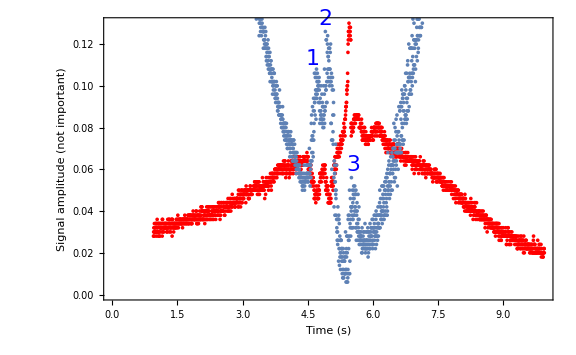
```mathematica
{1.6742155864124218*^7 (ï.8e£)^13 Null^9 -Graphics-,1360.7190892712197 (ï.8e£)^13 Null^9 -Graphics-}
```

{1.67422×10^7 (ï.8e£)^13 Null^9 -Graphics-,1360.72 (ï.8e£)^13 Null^9 -Graphics-}

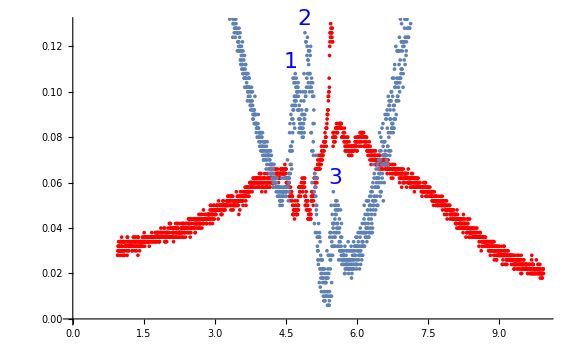

-Graphics-

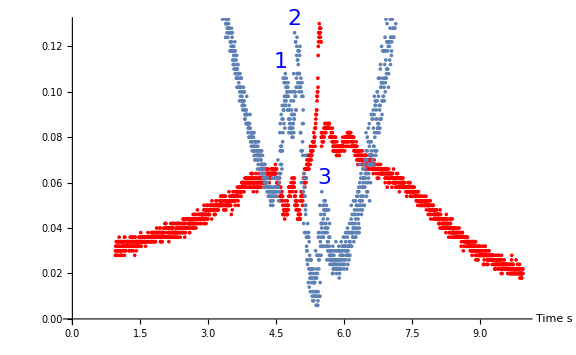

```mathematica
Show[%14,AxesLabel->{HoldForm[Time s],None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%15,PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

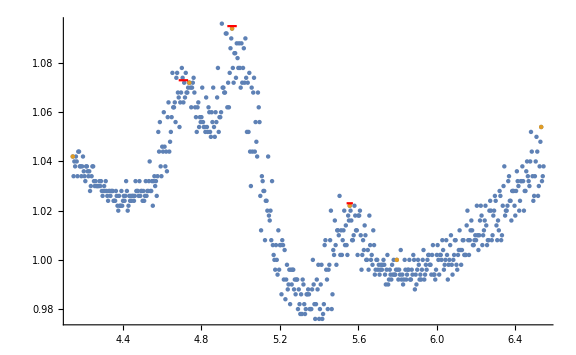

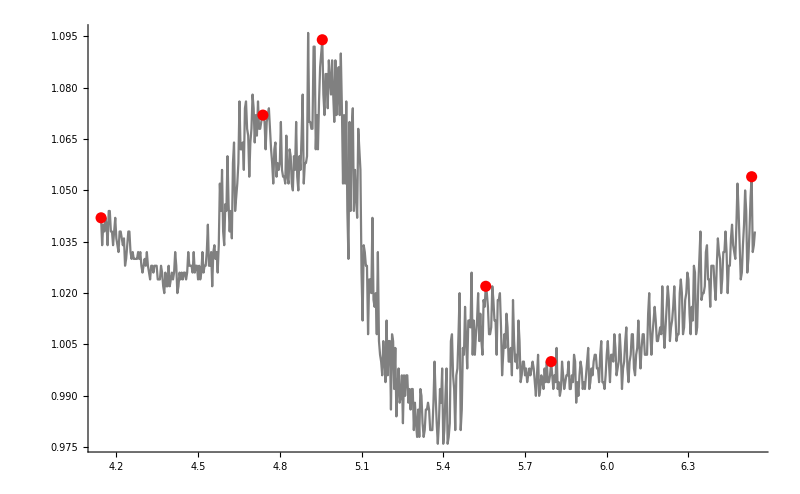

{4.738,4.956,5.556}

```mathematica
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
t = TimeSeries[las[[800;;1400]]];
Show[ListPlot[{t,FindPeaks[t,5.5]}],Plot[1.073,{x,4.708-0.024, 4.708+0.024},PlotStyle->Red],Plot[1.095,{x, 4.956-0.024,4.956+0.024},PlotStyle->Red],Plot[1.023,{x, 5.556-0.016,5.556+0.016},PlotStyle->Red],ImageSize->Large]ï.8e£Show[{ListLinePlot[t,PlotStyle->Gray],ListPlot[FindPeaks[t,5.5],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]ï.8e£FindPeaks[t,5.5]["PathTimes"][[2;;4]]
```

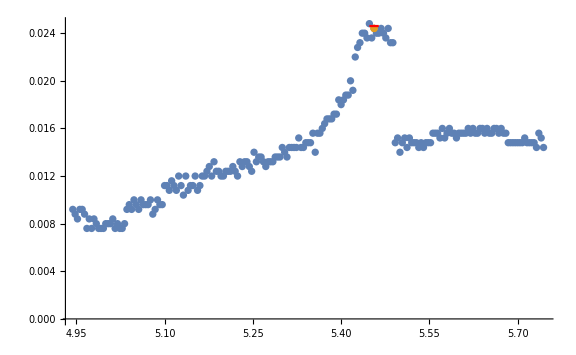

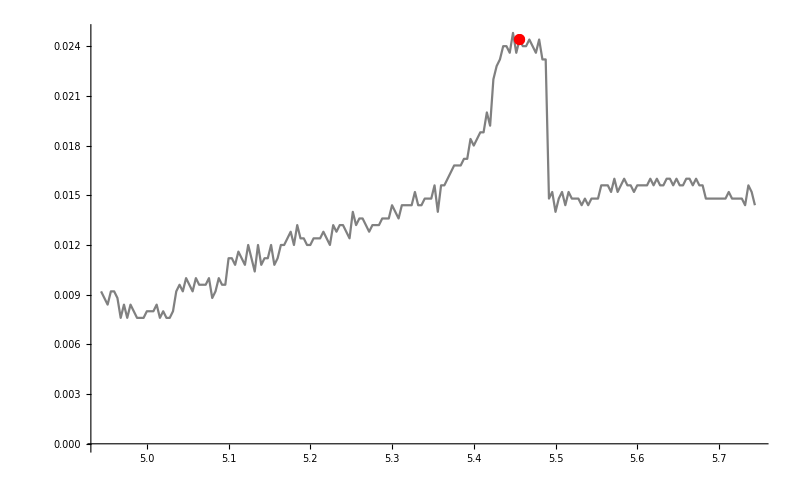

{5.456}

```mathematica
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
ï.8e£
ts = TimeSeries[pd[[1000;;1200]]];
ï.8e£
Show[ListPlot[{ts,FindPeaks[ts,100]}],Plot[0.0246,{x,5.456-0.008,5.456+0.008},PlotStyle->Red],ImageSize->Large]
ï.8e£
Show[{ListLinePlot[ts,PlotStyle->Gray],ListPlot[FindPeaks[ts,100],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
ï.8e£
FindPeaks[ts,100]["PathTimes"]
```

```mathematica
las2=Drop[Import["../osc/ALL0004/F0004CH1.CSV", {"Data", All, {4,5}}],-700];
pd2 = Drop[Drop[Import["../osc/ALL0004/F0004CH2.CSV",{"Data",All,{4,5}}],40],-700];ï.8e£Show[ListPlot[Map[{#[[1]],#[[2]]-0.01}&,pd2]],ListPlot[Map[{#[[1]],(#[[2]]-10.75) *0.1+0.005}&,las2],PlotStyle->Red],Graphics[{Green, Dashed, Thin,Line[{{2.344,0},{2.344,0.035}}]}],Axes -> {True, False}, Frame->{{True,False},{True,False}},FrameLabel->{Style["Time (s)",Medium],Style["Signal amplitude",Medium]},ï.8e£Graphics[{Green,Dashed, Thin,Line[{{3.986,0},{3.986,0.035}}]}],ï.8e£Graphics[{Orange,Dashed, Thin,Line[{{3.706,0},{3.706,0.035}}]}],ï.8e£Graphics[{Orange,Dashed, Thin,Line[{{2.064,0},{2.064,0.035}}]}],
ï.8e£PlotRange->{{0,7},{0,0.03}}]ï.8e£ts2 = TimeSeries[pd2];ï.8e£ts3 = TimeSeries[las2];ï.8e£FindPeaks[ts3,100]["PathTimes"]ï.8e£FindPeaks[ts2,100]["PathTimes",Frame->{{True,False},{True,False}},FrameLabel->{Style[x axis", Medium], 
  Style["y axis", 
   Medium]}, ImageSize -> Large]
```

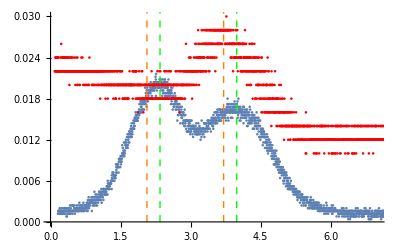

-Graphics-

```mathematica
{0.298,3.7060000000000004,7.166}
```

{0.298,3.706,7.166}

```mathematica
Î.93 = {2*Pi*6.0666, 2*Pi*0.0018};
ï.8e£
Is = {1.66932, 0.00035};
ï.8e£
PP = {10.6,0.05};
ï.8e£
w = {0.3021, 0.0061};
ï.8e£
Intensity[P_, ww_] := P/(Pi*ww^2/2);
ï.8e£
II = {Intensity[PP[[1]],w[[1]]] , Sqrt[D[Intensity[P,ww],{P,1}]^2*PP[[2]]^2 + D[Intensity[P,ww],{ww,1}]^2*w[[2]]^2]}/.{ww -> w[[1]], P -> PP[[1]]}
ï.8e£
Î.94Î.bd = {11.4161, 1.4423};
ï.8e£
RR[Î.931_,Is1_,II1_,Î.94Î.bd1_] := (Î.931)/2 *(II1/Is1)/(1+II1/Is1+((2 Î.94Î.bd1)/(Î.931))^2);
ï.8e£
R ={( (Î.93)/2 *(II/Is)/(1+II/Is+((2 Î.94Î.bd)/(Î.93))^2))[[1]], Sqrt[ D[RR[Î.931, Is1, II1, Î.94Î.bd1],{ Î.931,1}]^2 * Î.93[[2]]^2 + D[RR[Î.931, Is1, II1, Î.94Î.bd1],{ Is1,1}]^2 * Is[[2]]^2 + ï.8e£D[RR[Î.931, Is1, II1, Î.94Î.bd1],{ II1,1}]^2 * II[[2]]^2 +ï.8e£D[RR[Î.931, Is1, II1, Î.94Î.bd1],{ Î.94Î.bd1,1}]^2 * Î.94Î.bd[[2]]^2 ]}/. {Î.931 -> Î.93[[1]], Is1 -> Is[[1]], II1 -> II[[1]], Î.94Î.bd1 -> Î.94Î.bd[[1]]}
ï.8e£
diamLens = {0.025, 0.001};
ï.8e£
distMotLens = {0.105, 0.01};
ï.8e£
motPower = {0.168, 0.001};
ï.8e£
PMOT[rlens_, distance_, power_] = 4 distance^2/rlens^2 *power;
ï.8e£
totalPower = { PMOT[diamLens[[1]]/2, distMotLens[[1]],motPower[[1]]],Sqrt[D[PMOT[rlens, distance, power], {rlens, 1}]^2*(diamLens[[2]]/2)^2 + ï.8e£D[PMOT[rlens, distance, power],{distance, 1}]^2*distMotLens[[2]]^2 + D[PMOT[rlens, distance, power],{power, 1}]^2*motPower[[2]]^2],"total MOT power in Î.bcW" } /.{rlens -> diamLens[[1]]/2, distance->distMotLens[[1]], power->motPower[[1]]}
ï.8e£
h = 6.626070040*10^(â.88.9234);
ï.8e£
frequency = 3.8435*10^8;
ï.8e£
MotN[power_, scatteringRate_, Î.bd_] := power*10^(-6)/(scatteringRate*10^6*h*Î.bd*10^6);
ï.8e£
Population = {MotN[totalPower[[1]],R[[1]], frequency], Sqrt[D[MotN[power, scatteringRate, Î.bd],{power,1}]^2*totalPower[[2]]^2 + D[MotN[power, scatteringRate, Î.bd],{scatteringRate,1}]^2*R[[2]]^2]}/.{power->totalPower[[1]], scatteringRate->R[[1]],Î.bd->frequency}
```

{73.9409,3.00633}

{18.4915,0.0433621}

{47.4163,9.8,total MOT power in Î.bcW}

{1.00687×10^7,2.08113×10^6}